```mathematica
Clear["Global`*"]
```

```mathematica
inputData = Import[NotebookDirectory[]<>"/input.txt"];
input = StringSplit[inputData];
l=Length[input];(*l will have to be even*)
(*Write a function here that will take in strings as variable names*)
dt=Read[StringToStream[input[[2]]]];
tmax=input[[4]];
nStore=input[[6]];
nTrajectory=input[[8]];
nBin=input[[10]];
yWall=input[[12]];
lambda=input[[14]];
deltaZ=input[[16]];
deltaPz=input[[18]];
transitTime=input[[20]];
density=input[[22]];
rabi=input[[24]];
kappa=input[[26]];
invT2 = input[[28]];
controlType = input[[30]];
name =input[[32]]
```

dt0.01_dZ0_dPz0_tau1.0_nBin20_dens100_g3_k91

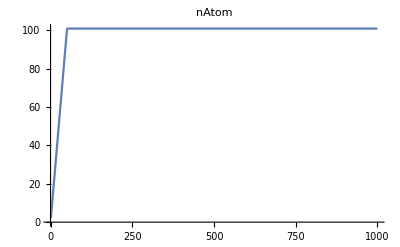

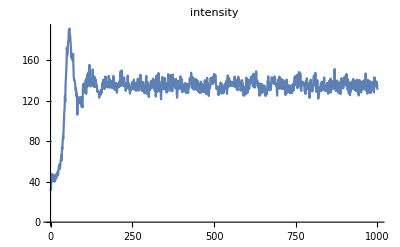

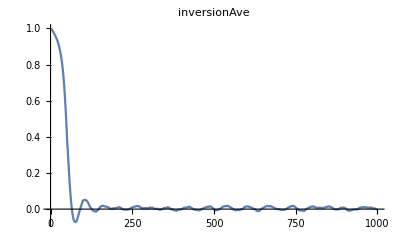

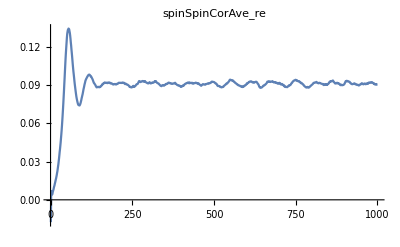

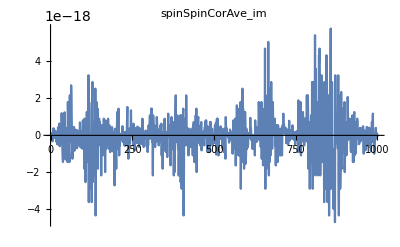

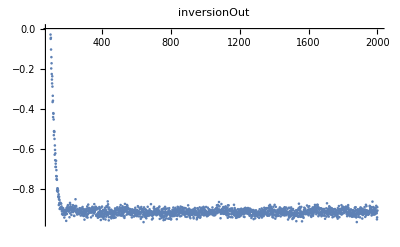

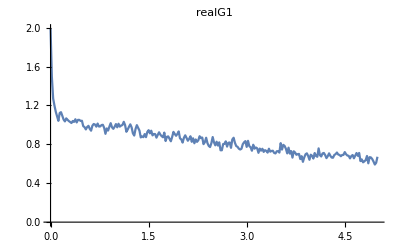

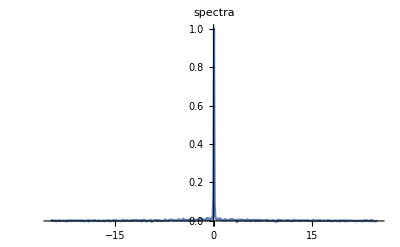

```mathematica
(*When doing one run*)
intensity=Flatten[Import[NotebookDirectory[]<>controlType <>"/"<>name<>"/intensity.dat"]];
nAtom=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/nAtom.dat"]];
inversionAve=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/inversionAve.dat"]];
spinSpinCorAveRe=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/spinSpinCorAve_re.dat"]];
spinSpinCorAveIm=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/spinSpinCorAve_im.dat"]];
spinSpinCorRe=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/spinSpinCor_re.dat"]];
spinSpinCorIm=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/spinSpinCor_im.dat"]];
szMatrix=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/szMatrix.dat"]];
szFinal=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/szFinal.dat"]];
realG1 = Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/realG1.dat"];
spectra=Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/spectra.dat"];
ListLinePlot[nAtom,PlotRange->All,PlotLabel->"nAtom"]
ListLinePlot[intensity,PlotRange->All,PlotLabel->"intensity"]
ListLinePlot[inversionAve,PlotRange->All,PlotLabel->"inversionAve"]
ListLinePlot[spinSpinCorAveRe,PlotRange->All,PlotLabel->"spinSpinCorAve_re"]
ListLinePlot[spinSpinCorAveIm,PlotRange->All,PlotLabel->"spinSpinCorAve_im"]
ListPlot[szFinal,PlotRange->All,PlotLabel->"inversionOut"]
ListLinePlot[realG1,PlotRange->All,PlotLabel->"realG1"]
ListLinePlot[spectra,PlotRange->All,PlotLabel->"spectra"]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[0.00565766/(0.0000112213+4 x^2)]

| Estimate | Standard Error | t-Statistic | P-Value
linewidth | 0.00334983 | 0.472122 | 0.00709527 | 0.994342
A | 1.68894 | 237.509 | 0.00711106 | 0.994329

0.00334983

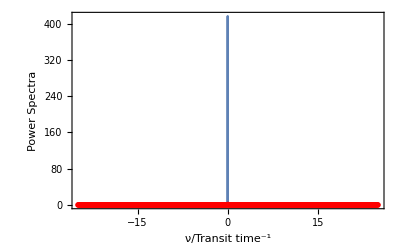

```mathematica
(*Fit the spectra to lorentzian*)
lorentzianModel=A linewidth/(linewidth^2+4x^2);
fitLoren=NonlinearModelFit[spectra,{lorentzianModel},{linewidth,A},{x}]
fitLoren["ParameterTable"]
linewidth1 = linewidth/.fitLoren["BestFitParameters"]
Show[{Plot[fitLoren[x],{x,-5,5},PlotRange->All,BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.01],Map[Point,spectra]}]},Frame->True,FrameLabel->{"ν/Transit time^-1","Power Spectra"}]
```

```mathematica
tauc1=1/(linewidth1 Pi)
```

95.0227

B ⅇ^(-t/tc)

FittedModel[1.11141 ⅇ^(-0.11839 t)]

| Estimate | Standard Error | t-Statistic | P-Value
tc | 8.44669 | 0.270293 | 31.2501 | 3.81021×10^-88
B | 1.11141 | 0.0103275 | 107.617 | 8.84414×10^-211

8.44669

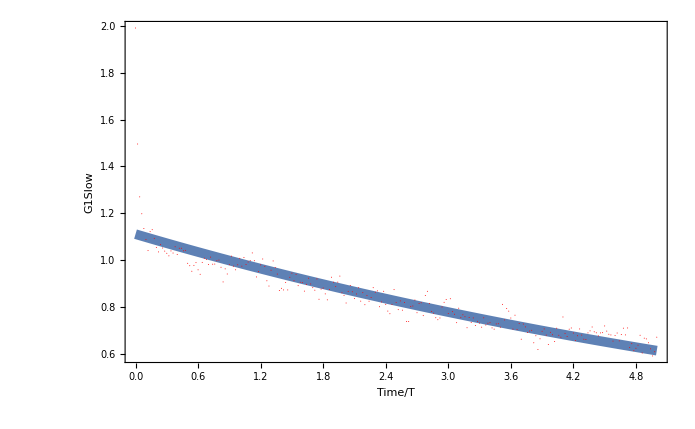

```mathematica
(*Fit the G1 function to exponential*)
exponentialModel=B Exp[- t/tc]
fitExp=NonlinearModelFit[realG1,{exponentialModel},{tc,B},{t}]
fitExp["ParameterTable"]
tauc2=tc/.fitExp["BestFitParameters"]
Show[{Plot[fitExp[x],{x,0,Last[realG1][[1]]},PlotRange->All,PlotStyle->{Thickness[0.01]},BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.01],Map[Point,realG1]}]},Frame->True,FrameLabel->{"Time/T","G1Slow"}]
```

```mathematica
(*Get the linewidth from the coherent time*)
linewidth2 = 1/(tauc2 Pi)
```

0.0376846

```mathematica
(*Notice there is another exponential decay.*)
```

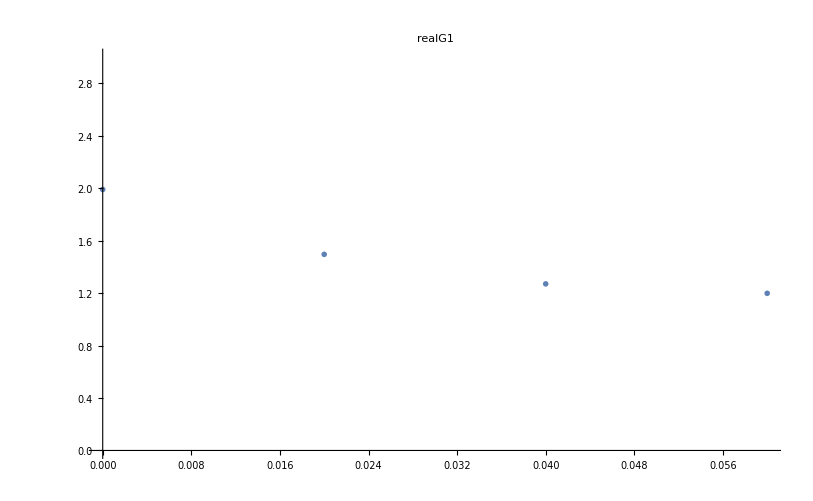

B2 ⅇ^(-linewidthQuick π t)

FittedModel[1.96609 ⅇ^(-11.6849 t)]

| Estimate | Standard Error | t-Statistic | P-Value
linewidthQuick | 3.71943 | 0.557224 | 6.67492 | 0.0946708
B2 | 1.96609 | 0.0718054 | 27.3808 | 0.0232403

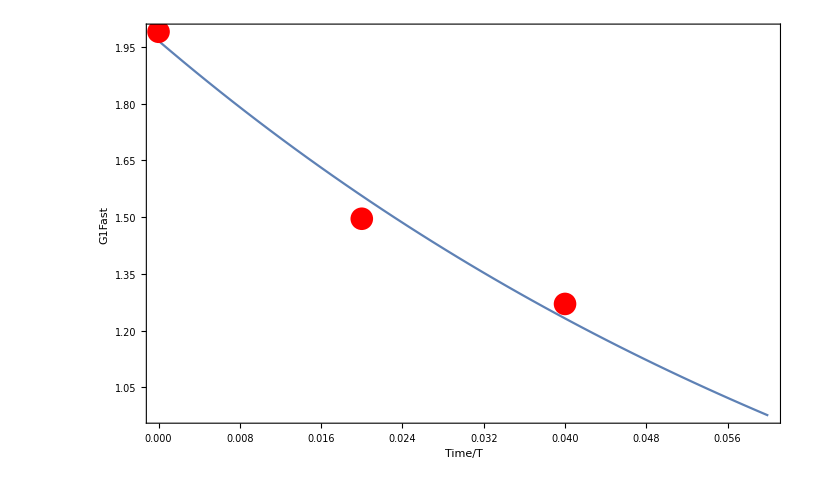

```mathematica
cutOff = 0.06;
ListPlot[realG1,PlotRange->{{0,cutOff},{0,3}}, 
PlotLabel->"realG1",PlotMarkers->{Automatic,Small}]
secondNum=IntegerPart[cutOff/realG1[[2,1]]];
secondExp=Take[realG1,secondNum];
exponentialModel2=B2 Exp[- Pi linewidthQuick t]
fitExp2=NonlinearModelFit[secondExp,{exponentialModel2},{linewidthQuick,B2},{t}]
fitExp2["ParameterTable"]
Show[{Plot[fitExp2[x],{x,0,cutOff},PlotRange->All,BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.02],Map[Point,secondExp]}]},Frame->True,FrameLabel->{"Time/T","G1Fast"}]
```

```mathematica
secondTc = 1/(linewidthQuick Pi)/.fitExp2["BestFitParameters"]
```

0.0855804

```mathematica
Mean[intensity]
```

132.563

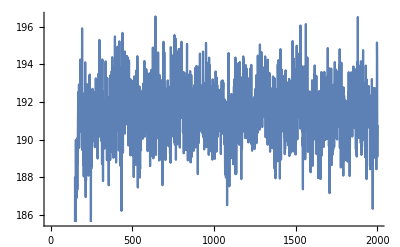

```mathematica
ListLinePlot[ 100*(1-szFinal)]
```

```mathematica
???
```

p?test is a pattern object that stands for any expression that matches p, and on which the application of test gives True.

Attributes[PatternTest]={HoldRest,Protected}